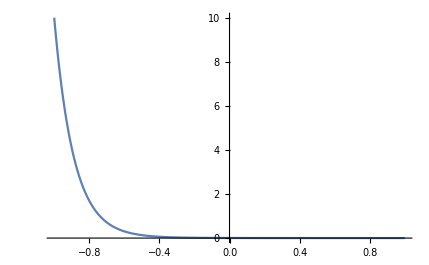

```mathematica
a = 1.0;
b =  0.1;
altitude = 100.0;
hitDistance = 100.0;
density[dy_]:= a  Exp[-b * altitude] (1 - Exp[-b * dy * hitDistance]) / (b * dy);
Plot[density[x], {x, -1.0, 1 }, PlotRange->Full]
```

```mathematica
beckman[a_,m_]:= Exp[-(Tan[a]/m)^2] / (4*Pi*m^2);
Manipulate[Plot[beckman[a,m], {a,0.0,π/2},PlotRange->Full],{m,1/100,π/2}]
```